# MATH224: Homework 7

## Plots all made by Trevor Swan.

NOTE: Please Indicate the which graph is which on the x(t) and y(t) graphs. If you ever doubt formatting, check the textbook solutions and use them as a reference.

## Question 3.3.19

The graphs for this question are a good example of what I’m referencing in the note beneath the title :)

### Initial Condition A

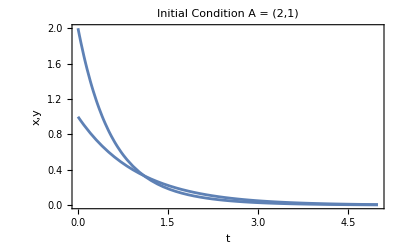

```mathematica
(* Plot for Initial Condition A = (2, 1) *)
component1x = Plot[(3/2)*Exp[-2*t]+(1/2)*Exp[-t],{t, 0,5}, PlotRange->{Automatic,{0,2}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition A = (2,1)"];
component1y = Plot[Exp[-t],{t, 0,5}, PlotRange->{Automatic,{0,2}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

### Initial Condition B

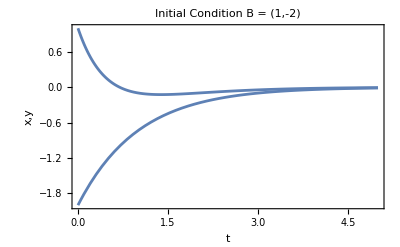

```mathematica
(* Plot for Initial Condition B = (1, -2) *)
component1x = Plot[2*Exp[-2*t]-Exp[-t],{t, 0,5}, PlotRange->{Automatic,{-2,1}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition B = (1,-2)"];
component1y = Plot[-2*Exp[-t],{t, 0,5}, PlotRange->{Automatic,{-2,1}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

### Initial Condition C

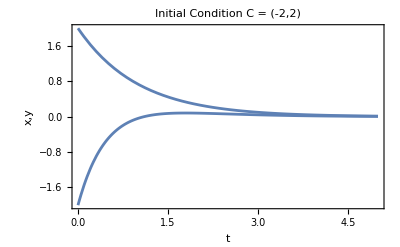

```mathematica
(* Plot for Initial Condition C = (-2, 2) *)
component1x = Plot[-3*Exp[-2*t]+Exp[-t],{t, 0,5}, PlotRange->{Automatic,{-2,2}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition C = (-2,2)"];
component1y = Plot[2*Exp[-t],{t, 0,5}, PlotRange->{Automatic,{-2,2}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

### Initial Condition D

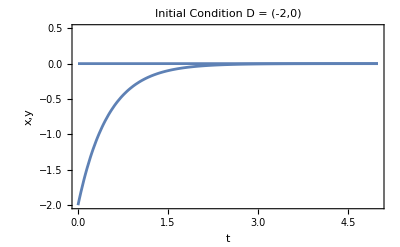

```mathematica
(* Plot for Initial Condition D = (-2, 0) *)
component1x = Plot[-2*Exp[-2*t],{t, 0,5}, PlotRange->{Automatic,{-2,0.5}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition D = (-2,0)"];
component1y = Plot[0,{t, 0,5}, PlotRange->{Automatic,{-2,0.5}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

## Question 3.3.23

### Incomplete Phase Portrait - Draw Solution Curves

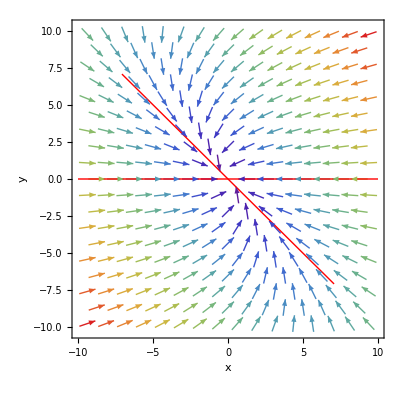

```mathematica
(* Set up Eigenvectors for part c *)
parentPlot =VectorPlot[{-0.2*x+-0.1*y,0*x+-0.1*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{-0.2,-0.1},{0,-0.1}}];
eigenLines1=Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(10*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(-10*eigenVectors)}];
(* Display the plot for c *)
Show[parentPlot,eigenLines1, eigenLines2, PlotRange-> All]
```

## Question 3.3.25

### Incomplete Phase Portrait - Draw Solution Curves

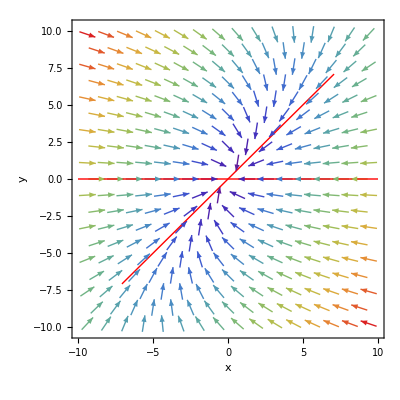

```mathematica
(* Set up Eigenvectors for part c *)
parentPlot =VectorPlot[{-0.2*x+0.1*y,0*x-0.1*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{-0.2,0.1},{0,-0.1}}];
eigenLines1=Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(10*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(-10*eigenVectors)}];
(* Display the plot for c *)
Show[parentPlot,eigenLines1, eigenLines2, PlotRange-> All]
```

## Question 3.3.27

```mathematica
(* Calculation for 27 part d, assume t >= 0 *)
NSolve[1==Sqrt[0.000025*Exp[-4*t]+0.000425*Exp[4*t]-0.00005],t, Reals]
```

{{t→-2.64917},{t→1.94087}}

## Question 3.4.3

### Phase Portrait - Indicate Direction of Curves!

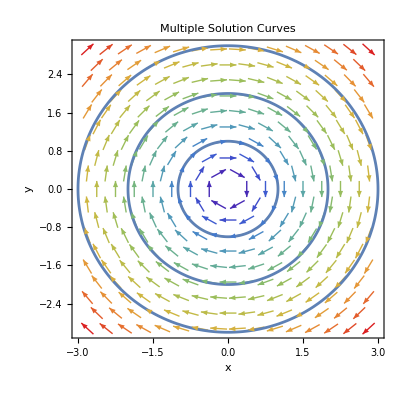

```mathematica
(* Vector Field and Multiple Curves for e *)
parentPlot =VectorPlot[{-0*x+2*y,-2*x+0*y},{x,-3,3},{y,-3,3},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow",PlotLabel->"Multiple Solution Curves"];
solutionCurve1 = ParametricPlot[{Cos[2t],-Sin[2t]},{t,0,Pi}];
solutionCurve2 = ParametricPlot[{2*Cos[2t],-2*Sin[2t]},{t,0,Pi}];
solutionCurve3 = ParametricPlot[{3*Cos[2t],-3*Sin[2t]},{t,0,Pi}];
Show[parentPlot, solutionCurve1,solutionCurve2, solutionCurve3]
```

### x(t) and y(t) Graphs

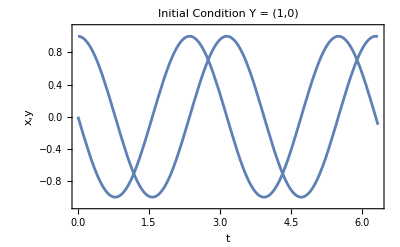

```mathematica
(* Plot for Initial Condition Y = (1, 0) *)
component1x = Plot[Cos[2t],{t, 0,2*Pi+0.05}, PlotRange->{Automatic,{-1.1,1.1}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition Y = (1,0)"];
component1y = Plot[-Sin[2t],{t, 0,2*Pi+0.05}, PlotRange->{Automatic,{-1.1,1.1}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

## Question 3.4.7

### Calculate Eigenvectors bc I’m Lazy

```mathematica
(* Calculate Eigenvectors for e *)
eigenVectors=Eigenvectors[{{2,-6},{2,1}}]
```

{{1/4 ⅈ (-ⅈ+√47),1},{-1/4 ⅈ (ⅈ+√47),1}}

### Incomplete Phase Portrait - Draw Solution Curves

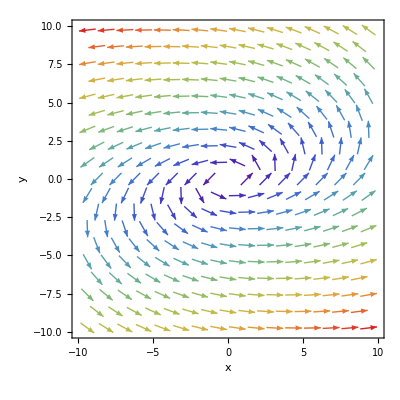

```mathematica
(* Vector Field for d, Not bothered with plotting all the Curves. Do it by hand! *)
VectorPlot[{2*x+-6*y,2*x+1*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"]
```

```mathematica
(* Solve for k_1 and k_2 *)
N[Solve[k1*(1/4)*(Cos[0*Sqrt[47]/2]-Sqrt[47]*Sin[0*Sqrt[47]/2])+k2*(Sin[0*Sqrt[47]/2]+Sqrt[47]*Cos[0*Sqrt[47]/2])==2 && k1*Cos[0*Sqrt[47]/2]+k2*Sin[0*Sqrt[47]/2]==1,{k1,k2}]]
```

{{k1→1.,k2→0.255264}}

### x(t) and y(t) Graphs

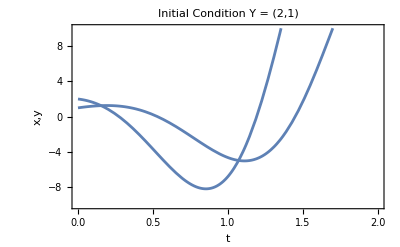

```mathematica
component1x = Plot[Exp[3t/2]*((1/4)*(Cos[t*Sqrt[47]/2]-Sqrt[47]*Sin[t*Sqrt[47]/2])+0.255264*(Sin[t*Sqrt[47]/2]+Sqrt[47]*Cos[t*Sqrt[47]/2])),{t, 0,2}, PlotRange->{Automatic,{-10,10}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition Y = (2,1)"];
component1y = Plot[Exp[3t/2]*(Cos[t*Sqrt[47]/2]+0.255264*Sin[t*Sqrt[47]/2]),{t, 0,2}, PlotRange->{Automatic,{-10,10}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

## Question 3.4.11

### x(t) and y(t) Graphs

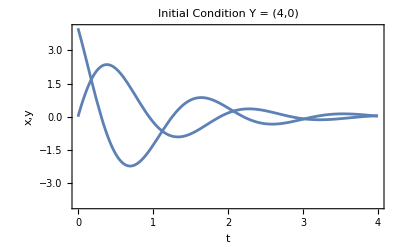

```mathematica
(* Plot for x and y graphs for Y = (4,0)*)
component1x = Plot[(4/Sqrt[11])*Exp[-t]*(-2*Sin[Sqrt[11]*t]+Sqrt[11]*Cos[Sqrt[11]*t]),{t, 0,4}, PlotRange->{Automatic,{-4,4}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition Y = (4,0)"];
component1y = Plot[(4/Sqrt[11])*Exp[-t]*(3*Sin[Sqrt[11]*t]),{t, 0,4}, PlotRange->{Automatic,{-4,4}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

## Question 3.5.3

### Just a Complete Direction Plot

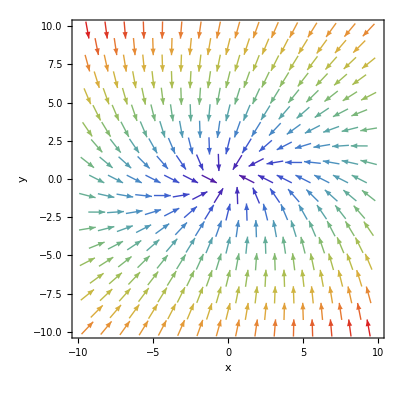

```mathematica
(* Plot the Direction Field for the System *)
VectorPlot[{-2*x+-1*y,1*x+-4*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"]
```

### Incomplete Phase Portrait - Draw Solution Curves

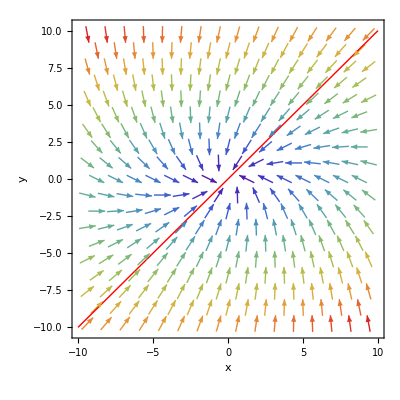

```mathematica
(* Vector Field and Eigenvector. Plot Solution Curves by Hand *)
parentPlot =VectorPlot[{-2*x+-1*y,1*x+-4*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{-2,-1},{1,-4}}];
eigenLines1=Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(10*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(-10*eigenVectors)}];
(* Display the plot for d *)
Show[parentPlot,eigenLines1, eigenLines2, PlotRange-> All]
```

## Question 3.5.7

### x(t) and y(t) Graphs

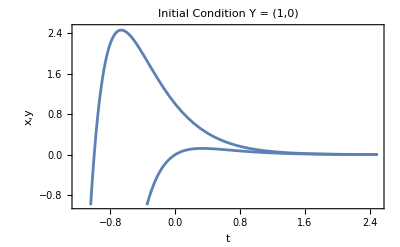

```mathematica
(* Plot for x and y graphs for Y = (1,0)*)
component1x = Plot[Exp[-3*t]+t*Exp[-3*t],{t, -1.2,2.5}, PlotRange->{Automatic,{-1,2.5}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition Y = (1,0)"];
component1y = Plot[t*Exp[-3*t],{t, -1.2,2.5}, PlotRange->{Automatic,{-1,2.5}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

## Question 3.5.19

### Incomplete Phase Portrait - Draw Solution Curves

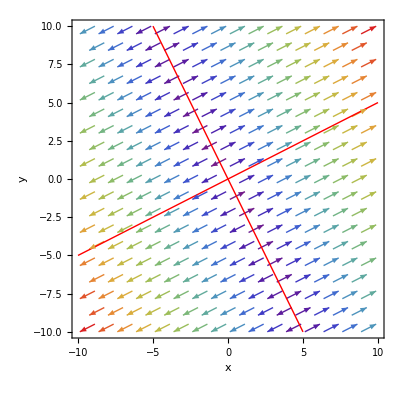

```mathematica
(* Vector Field and Eigenvector. Plot Solution Curves by Hand *)
parentPlot =VectorPlot[{4*x+2*y,2*x+1*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{4,2},{2,1}}];
eigenLines1=Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(5*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(-5*eigenVectors)}];
(* Display the plot for c *)
Show[parentPlot,eigenLines1, eigenLines2, PlotRange-> All]
```

### x(t) and y(t) Graphs

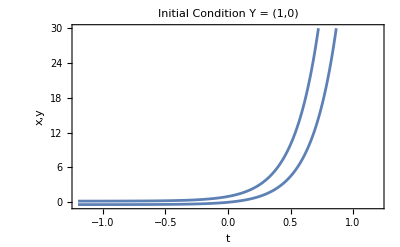

```mathematica
(* Use Part e to create plot for part f *)
component1x = Plot[(1/5)+(4/5)*Exp[5*t],{t, -1.2,1.2}, PlotRange->{Automatic,{-.5,30}},Frame->True,FrameLabel->{"t","x,y"}, PlotLabel->"Initial Condition Y = (1,0)"];
component1y = Plot[-(2/5)+(2/5)*Exp[5*t],{t, -1.2,1.2}, PlotRange->{Automatic,{-.5,30}}];
(* Display the Plot Needed *)
Show[component1x, component1y]
```

## Question 3.5.21

### Incomplete Phase Portrait - Draw Solution Curves

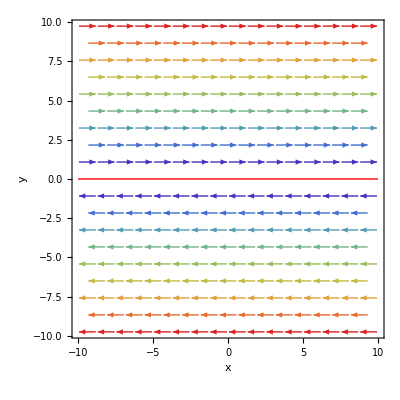

```mathematica
(* Vector Field and Eigenvector. Plot Solution Curves by Hand *)
parentPlot =VectorPlot[{0*x+2*y,0*x+0*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{0,2},{0,0}}];
eigenLines1=Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(10*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(-10*eigenVectors)}];
(* Display the plot for a *)
Show[parentPlot,eigenLines1, eigenLines2, PlotRange-> All]
```

### Incomplete Phase Portrait - Draw Solution Curves

{{1,0},{0,0}}

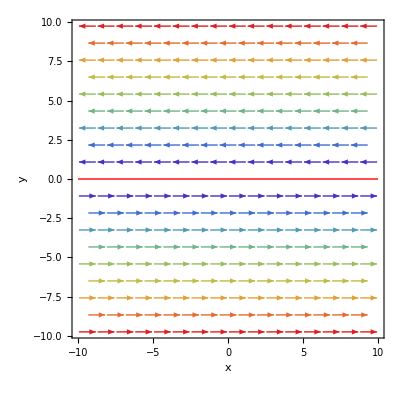

```mathematica
(* Vector Field and Eigenvector. Plot Solution Curves by Hand *)
parentPlot =VectorPlot[{0*x+-2*y,0*x+0*y},{x,-10,10},{y,-10,10},VectorPoints->Medium,Axes->True,AxesLabel->{"x","y"},VectorColorFunction->"Rainbow"];
eigenVectors=Eigenvectors[{{0,-2},{0,0}}];
eigenLines1=Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(10*eigenVectors)}];
eigenLines2 = Graphics[{Red,Arrowheads[0],Arrow[{{0,0},#}]&/@(-10*eigenVectors)}];
(* Display the plot for b *)
Show[parentPlot,eigenLines1, eigenLines2, PlotRange-> All]
```

```mathematica
Eigenvectors[{{-2, 0, 0},{-2, 0, 2},{0, 0, -2}}]
Eigenvalues[{{-2, 0, 0},{-2, 0, 2},{0, 0, -2}}];
```

{{1,0,1},{1,1,0},{0,1,0}}